```mathematica
"Project Thesis Superconductors"
"Anayltical Fermi-Dirac Distribution, Entropy and Heat Capacity Calculation"
"Author: Christoph Bernkopf"
```

Project Thesis Superconductors

Anayltical Fermi-Dirac Distribution, Entropy and Heat Capacity Calculation

Author: Christoph Bernkopf

```mathematica
(* Clear all variables as follows: *)
(* ClearAll["Global`*"] *)

(* Load Numerical Calculus Package *)
<<NumericalCalculus`

(* Constants *)
	kB=1.3806482*10^(-23); (* Boltzmann Constant *)
	Tc=2.05;
	AlphaBCS=1.764;
	gamma=1*kB;

(* Experimental Data *)
	jGap=Import["Documents/coding/sl_code/data/johnson_band_gap_data.csv","CSV"];
	mGap  = Import["Documents/coding/sl_code/data/muehlschlegel_data_Bandgap.csv","CSV"];
	mEnt= Import["Documents/coding/sl_code/data/muehlschlegel_data_Entropy.csv","CSV"];
	mHCap= Import["Documents/coding/sl_code/data/muehlschlegel_data_Heat_Capacity.csv","CSV"];
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

| Estimate | Standard Error | t-Statistic | P-Value
a | -4.06181 | 1.20045 | -3.38358 | 0.00190474
b | -4.07055 | 1.19382 | -3.40969 | 0.00177613
c | 11.4969 | 3.97224 | 2.89431 | 0.00678997
d | 11.6771 | 3.85625 | 3.02811 | 0.00483434
e | -16.5437 | 8.11781 | -2.03795 | 0.049892
f | -17.9131 | 7.3349 | -2.44217 | 0.0203048
g | 7.92016 | 11.8554 | 0.668064 | 0.508883
h | 12.3709 | 9.4388 | 1.31064 | 0.199308
i | 2.14757 | 9.3539 | 0.229591 | 0.819871
j | -3.16789 | 6.4985 | -0.48748 | 0.629241
k | -1.95907 | 2.81103 | -0.696923 | 0.490883
l | 0.10439 | 1.70306 | 0.0612954 | 0.951505

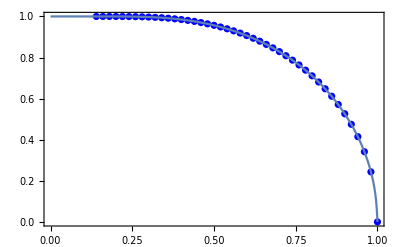

```mathematica
(* Band Gap Fit *)
deltaFit = NonlinearModelFit[mGap,(1+a*T+c*T^2+e*T^3+g*T^4+i*T^5+k*T^6)/(1+b*T+d*T^2+f*T^3+h*T^4+j*T^5+l*T^6),{a,b,c,d,e,f,g,h,i,j,k,l},T];
deltaFit["ParameterTable"]

(* Band Gap Plot in Comparison with Muelschlegel Data *)	
Show[ListPlot[mGap, PlotStyle->Blue], Plot[deltaFit[T],{T,0,1}],Frame->True]
```

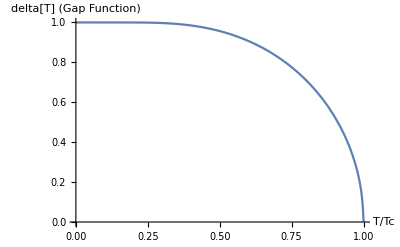

```mathematica
(* Band Gap Plot *)
	Plot[deltaFit[T],{T,0,1.}, AxesLabel->{"T/Tc", "delta[T] (Gap Function)"}]
```

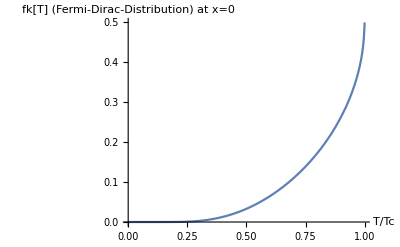

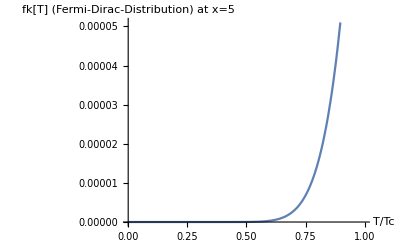

```mathematica
(* Fermi-Dirac-Distribution *)
	(* Units: None *)
	fx[T_,x_]:=(Exp[AlphaBCS/T*(x^2+deltaFit[T]^2)^(1/2)]+1)^(-1);

(* Fermi-Dirac-Distribution Plot *)
Plot[fx[T,0],{T,0,1.}, AxesLabel->{"T/Tc", "fk[T] (Fermi-Dirac-Distribution) at x=0"}]

(* Fermi-Dirac-Distribution Plot *)
Plot[fx[T,5],{T,0,1.}, AxesLabel->{"T/Tc", "fk[T] (Fermi-Dirac-Distribution) at x=5"}]
```

```mathematica
(* Electronic Entropy *)
	(* Entropy INTEGRAL based calculation *)
	Ses[T_]:=-6*AlphaBCS/Pi^2*NIntegrate[fx[T,x]*Log[fx[T,x]]+(1-fx[T,x])*Log[1-fx[T,x]],{x,0,100}];
```

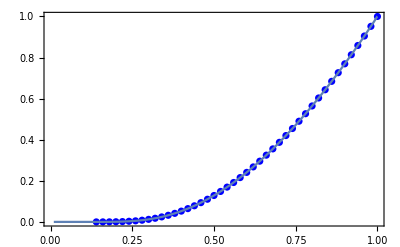

```mathematica
(* Electronic Entropy Plot *)
	(* Plot[Ses[T],{T,0.01,1.}, AxesLabel->{"T/Tc", "Ses[T] (Electronic Entropy)"}] *)
	Show[ListPlot[mEnt, PlotStyle->Blue], Plot[Ses[T],{T,0.01,1.}, AxesLabel->{"T/Tc", "Ses[T] (Electronic Entropy)"}],Frame->True]
```

```mathematica
(* Heat Capacity *)
	Ces[T_]:=T*Ses'[T];
```

NIntegrate::inumr: The integrand Log[1/(1+ⅇ^(1.764 Power[«2»] Power[«2»]))]/(1+ⅇ^((1.764 √Plus[«2»])/Slot[«1»]))+(1-1/(1+ⅇ^Times[«3»])) Log[1-1/(1+Power[«2»])] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,100}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

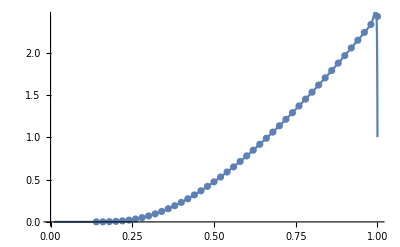

```mathematica
(* Heat Capacity Plot *)
	Show[ListPlot[mHCap],Plot[Ces[T],{T,0.01,1.}]]
```

```mathematica
"Difference between peak and base line at 1"
Ces[0.99]-Ces[1]
```

Difference between peak and base line at 1

NIntegrate::inumr: The integrand Log[1/(1+ⅇ^(1.764 Power[«2»] Power[«2»]))]/(1+ⅇ^((1.764 √Plus[«2»])/Slot[«1»]))+(1-1/(1+ⅇ^Times[«3»])) Log[1-1/(1+Power[«2»])] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,100}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

1.45424